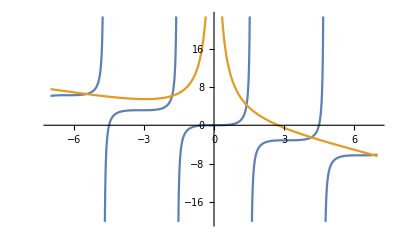

```mathematica
Plot[{{s},{Sqrt[(8/z)^2-1]-z}},{z,-7,7}]
```

We can use Desmos to find the intersections. The intersections correspond to a z-value, which corresponds to an energy eigenvalue. Since there are 5 intersections we know there will be 5 even eigenfunctions (we know they are even since we found them with the condition A=0).

```mathematica
Integrate[(Sqrt[2]/a)*Cos[3*Pi*x/(2*a)]*Cos[Pi*x/a],{x,-a/2,a/2}]
```

8/(5 π)

```mathematica
DSolve[-psi''[z]+k1*z*psi[z]==k2*psi[z],psi[z],z]
```

{{psi[z]→AiryAi[(-k2+k1 z)/k1^(2/3)] C[1]+AiryBi[(-k2+k1 z)/k1^(2/3)] C[2]}}

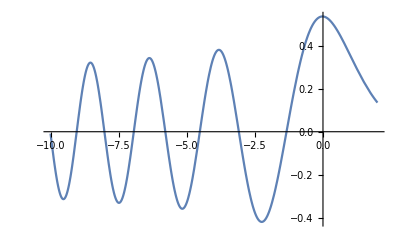

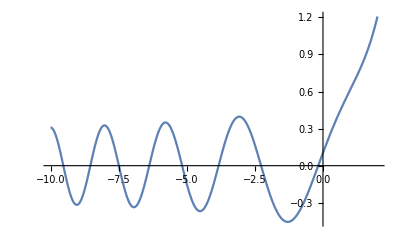

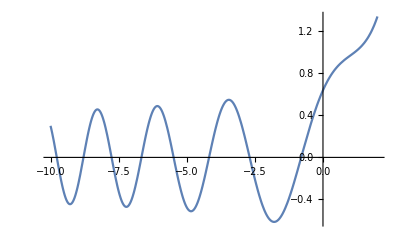

```mathematica
k1 = 1;
k2 = 1;
A = 1;
B=1;
Plot[AiryAi[(-k2+k1 z)/k1^(2/3)]*A,{z,-10,2}]
Plot[AiryBi[(-k2+k1 z)/k1^(2/3)]*B,{z,-10,2}]
Plot[AiryAi[(-k2+k1 z)/k1^(2/3)]*A+AiryBi[(-k2+k1 z)/k1^(2/3)]*B,{z,-10,2}]
```

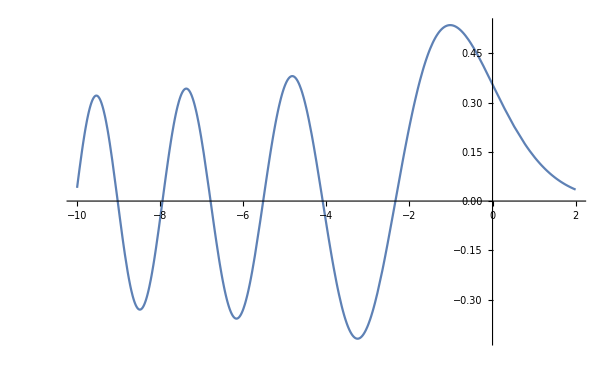

1/(3^(2/3) Gamma[2/3])

```mathematica
(* we can approximate the zeros with *)
Plot[AiryAi[z]*A,{z,-10,2}]
```

```mathematica
NIntegrate[AiryAi[-2.4+z]^2,{z,0,∞}]
```

0.491735

```mathematica
Sqrt[1/0.4917354066126901]
```

1.42605

```mathematica
NIntegrate[z*AiryAi[-2.4+z]^2,{z,0,∞}]
```

0.796859

```mathematica
(1.426^2)*0.7968593148382319
```

1.62039

FindRoot::nveq: The number of equations does not match the number of variables in (-k2 + k1\ z)/k1^Times[«2»](-k2 + k1\ z)/k1^Times[«2»].